```mathematica
(* ILT function which can handle shifting with θ and also a list of time points in T *)
ILT[fun_, T_, maxFnEvals_, method_:"cme",θ_:0,precision_:MachinePrecision]:=Module[{params,i,η,β,ξ,n,k,prec},
If[Min[T]<0,Print["T should be non-negative!!!"];Return[0]]; 

If[Length[Position[Names["Global`*"],"cmeParams"]]==0 || Length[cmeParams]==0,
(*Print["CME parameters loaded"];*)
cmeParams = Import[FileNameJoin[{NotebookDirectory[],"iltcme.json"}]];
];
If[precision≤15,prec=MachinePrecision,prec=precision];
If[method=="cme",
params = cmeParams[[1]];
For[i=2,i<Length[cmeParams],i++,
If[("cv2"/.cmeParams[[i]]) <("cv2"/.params) && ("n"+1 /.cmeParams[[i]])≤maxFnEvals,params=cmeParams[[i]] ]
];
η=SetPrecision[Prepend["a"*"mu1"+ⅈ*"b"*"mu1"/.params,"c"*"mu1"/.params],prec];
β=SetPrecision[Prepend[1+ⅈ * "omega"*Range["n"/.params],1]*"mu1" /.params,prec];
,
If[method=="euler",
n=If[Mod[maxFnEvals,2]==0,maxFnEvals-1,maxFnEvals];
β=Table[SetPrecision[((n-1)Log[10])/6+π ⅈ (k-1),prec],{k,1,n}];
ξ=ConstantArray[SetPrecision[1,prec],n];
ξ[[1]] = SetPrecision[1/2,prec];
ξ[[n]]=SetPrecision[1/2^((n-1)/2),prec];
For[k=1,k<(n-1)/2,k++,ξ[[n-k]]=ξ[[n-k+1]]+ 2^(-(n-1)/2)Binomial[(n-1)/2,k]];
η=Table[SetPrecision[10^((n-1)/6)(-1)^(k-1)ξ[[k]],prec],{k,1,n}];
];
];
Return[If[ListQ[T],Table[Re[Sum[Exp[θ]*η[[k]]*fun[(β[[k]]+θ)/x],{k,1,Length[η]}]/x],{x,T}],
Re[Sum[Exp[θ]*η[[k]]*fun[(β[[k]]+θ)/T],{k,1,Length[η]}]/T]]];
];
```

```mathematica
(* optimized ILT function handles only a single time point *)
ILTopt[fun_, T_, maxFnEvals_, θmin_:0,θmax_:10^8,method_:"cme",precision_:MachinePrecision,θeps_:10^(0)]:=Module[{m0,m1,m2,m3,θl,θ,niltcount,m1nilt,m2nilt,goldenratio,maxiter,prec},
If[ListQ[T],Print["T should be a single time point!!!"];Return[0]]; 
If[precision≤15,prec=MachinePrecision,prec=precision];

m0=θmin;
m3=θmax;
goldenratio=(√5-1)/2;
(* golden ratio search *)
m1=goldenratio * m0+(1-goldenratio)*m3;
m2=(1-goldenratio) * m0+goldenratio*m3;

m1nilt=Max[ILT[fun,T,maxFnEvals,"cme",m1,prec]];

m2nilt=Max[ILT[fun,T,maxFnEvals,"cme",m2,prec]];
niltcount=2; (* NILT evaluation counter *)
maxiter = 50;
While[(Abs[m3-m0]>θeps)&&(niltcount<maxiter),
niltcount = niltcount +1;
(* Print["θl=", m0//N ,", θh=",m3//N, ", m1=", m1//N ,", m2=",m2//N, ", h_N(m1)=", m1nilt//N ,", h_N(m2)=",m2nilt//N]; *)
If[m1nilt≤m2nilt,
m3=m2;m2=m1;m1=goldenratio * m0+(1-goldenratio)*m3;m2nilt=m1nilt;m1nilt=Max[ILT[fun,T,maxFnEvals,"cme",m1,prec]];
,
m0=m1;m1=m2;m2=(1-goldenratio) * m0+goldenratio*m3;m1nilt=m2nilt;m2nilt=Max[ILT[fun,T,maxFnEvals,"cme",m2,prec]];
];
If[Precision[m1nilt]<10 ||Precision[m2nilt]<10, Print ["Precision loss!! Precision is ",Min[Precision[m1nilt],Precision[m2nilt]]];Return[0]]
];
If[niltcount==maxiter,Print["Does not converge in ",maxiter," iterations."]];
θ=(m0+m3)/2;
If[θ<0,
If[θ/θmin>0.95,Print["θ is close to the lower bound!!!"];Print["The number of NILT calls in NILTopt: ", niltcount, ", {θmin,θmax,θopt}=",{θmin, θmax, θ}//N];
]; 
If[θmax<0 &&θ/θmax<1.05,Print["θ is close to the upper bound!!!"];Print["The number of NILT calls in NILTopt: ", niltcount, ", {θmin,θmax,θopt}=",{θmin, θmax, θ}//N];
];
, (* θ>0 *)
If[θmin>0&&θ/θmin<1.05,Print["θ is close to the lower bound!!!"];Print["The number of NILT calls in NILTopt: ", niltcount, ", {θmin,θmax,θopt}=",{θmin, θmax, θ}//N];
]; 
If[θ/θmax>0.95,Print["θ is close to the upper bound!!!"];Print["The number of NILT calls in NILTopt: ", niltcount, ", {θmin,θmax,θopt}=",{θmin, θmax, θ}//N];
];
];
Print["The number of NILT calls in NILTopt: ", niltcount, ", {θmin,θmax,θopt}=",{θmin, θmax, θ}//N];
Return[ILT[fun,T,maxFnEvals,method,θ,prec]];
];
```

```mathematica
DSILThshift[fun_, T_, maxFnEvals_, θmin_:(-10^8),θmax_:10^8,hshift_:1,method_:"cme",precision_:MachinePrecision,θeps_:10^0]:=
Module[{Δ,Δfun,prec,Tprec},
If[precision≤15,prec=MachinePrecision,prec=precision];
If[Precision[T]<precision,Tprec=SetPrecision[T,prec],Tprec=T];
Δ=hshift-T;
If[Precision[Δ]<precision,Δ=SetPrecision[Δ,prec]];
Δfun=Function[s,fun[s] ⅇ^(-s Δ)];
Return[ILTopt[Δfun, hshift, maxFnEvals, θmin,θmax,method,prec,θeps]]
];
```

```mathematica
DSILTopt[fun_, T_, maxFnEvals_, θmin_:(-10^8),θmax_:10^8,method_:"cme",precision_:MachinePrecision,θeps_:10^(0)]:=
Module[{prec,Tprec,m0,m1,m2,δ,cv,f0,fδ,fmδ,hshift},
If[precision≤15,prec=MachinePrecision,prec=precision];
If[Precision[T]<precision,Tprec=SetPrecision[T,prec],Tprec=T];
(* Compute the variance *)
δ=10^-6;
If[Dimensions[Dimensions[fun[0]]][[1]]==2,f0=fun[0][[1,1]];fδ=fun[δ][[1,1]];fmδ=fun[-δ][[1,1]];
Print["DSILTopt is called with a list of dimensions ",Dimensions[fun[0]],", the shifting parameter is computed based on its [1,1] element." ],
f0=fun[0];fδ=fun[δ];fmδ=fun[-δ]
];

m0=f0;
m1=-(fδ-m0)/δ;
m2=(fδ-2m0+fmδ)/δ^2;
cv=Sqrt[m2/m0-(m1/m0)^2];
If[m2/m0-(m1/m0)^2<0,Print[ "Negative moment error !!!"];Print["T=",T,", m0=", m0//N ,", m1=",m1//N, ", m2=", m2//N ,", cv=",cv//N, ", scv=",cv^2//N, ", Hshift=",hshift//N];  Return[0]];


(* Compute the optimal shifting *)
hshift=cv/(1/4);
Print["T=",T,", m0=", m0//N ,", m1=",m1//N, ", m2=", m2//N ,", cv=",cv//N, ", scv=",cv^2//N, ", Hshift=",hshift//N]; 
Return[DSILThshift[fun, T, maxFnEvals, θmin,θmax,hshift,method,precision,θeps]
]
];
```

```mathematica
DSILToptRefined[fun_, T_, maxFnEvals_, θmin_:(-10^8),θmax_:10^8,method_:"cme",precision_:MachinePrecision,θeps_:10^(0)]:=
Module[{prec,Tprec,m0,m1,m2,δ,cv,f0,fδ,fmδ,hshift,pm1,p0,p1,a,p0r},
If[precision≤15,prec=MachinePrecision,prec=precision];
If[Precision[T]<precision,Tprec=SetPrecision[T,prec],Tprec=T];

(* Dimension check *)
If[Dimensions[Dimensions[fun[0]]][[1]]==2 || Dimensions[T]≠{},
Print["DSILToptRefined is called with a list of dimensions ",Dimensions[fun[0]]," at time points",T,". DSILToptRefined is applicable only for scalar functions at single time point!" ];
Return[0];
];

(* Compute the variance *)
δ=10^-6;
f0=fun[0];fδ=fun[δ];fmδ=fun[-δ];

m0=f0;
m1=-(fδ-m0)/δ;
m2=(fδ-2m0+fmδ)/δ^2;
cv=Sqrt[m2/m0-(m1/m0)^2];
If[m2/m0-(m1/m0)^2<0, Print[ "Negative moment error !!!"]; Print["T=",T,", m0=", m0//N ,", m1=",m1//N, ", m2=", m2//N ,", cv=",cv//N, ", scv=",cv^2//N, ", Hshift=",hshift//N]; Return[0] ];


(* Compute the optimal shifting *)
hshift=cv/(1/4);

(* refined the shifting approximation *)
δ=10^-6;
pm1 = DSILThshift[fun, T-δ, maxFnEvals, θmin,θmax,hshift,method,precision,θeps];
p0 = DSILThshift[fun, T, maxFnEvals, θmin,θmax,hshift,method,precision,θeps];
p1 = DSILThshift[fun, T+δ, maxFnEvals, θmin,θmax,hshift,method,precision,θeps];
a=(Log[pm1]-2 Log[p0]+Log[p1])/(2 δ^2);
If[a<-4, a =-4];
If[a<(- m0^2)/(2 m2 m0 - 2 m1^2), hshift=4 Sqrt[-1/(2 a) ];
p0r=DSILThshift[fun, T, maxFnEvals, θmin,θmax,hshift,method,precision,θeps]
,(* no refinement *)
p0r=p0];

Print["T=",T,", m0=", m0//N ,", m1=",m1//N, ", m2=", m2//N ,", Hshift=",4 cv//N, ", p_-1=",pm1//N, ", p_0=",p0//N, ", p_1=",p1//N, ", a=",a//N, ", HshiftRef=",hshift//N]; 
Return[{p0r,p0}
]
];
```

```mathematica
(* innet a vizsgalatokhoz keszitett fuggvenyek jonnek *)
```

```mathematica
PDF[NormalDistribution[m,Sqrt[s]],x]
```

(ⅇ^(-(-m+x)^2/(2 s)))/(√(2 π) √s)

```mathematica
(* normal distribution *)
mean=0.;
data={m->mean, s->3.};
fs2[v_]:= Exp[-v*m+v^2 *s/2]/.data
rese3=Table[{T,PDF[NormalDistribution[m,Sqrt[s]]/.data,T]//N},{T,-24,24,3}];
res3=Table[{T,DSILTopt[fs2, T,30,-1000,1000]},{T,-24,24,3}];
```

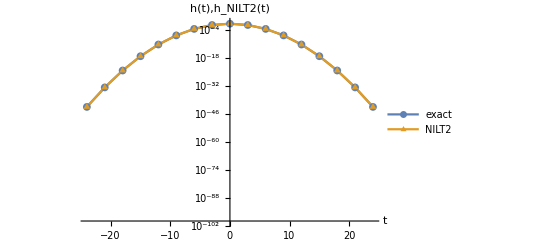

c:/temp/aa/norm_0_3.pdf

```mathematica
ListLogPlot[{rese3,res3},Joined->True,PlotRange->{10^-100,10^0},PlotMarkers->{{●,8},{▲,8}},PlotLegends->Placed[{"exact","NILT2"},{0.85,0.15}],AxesLabel->{"t","h(t),h_NILT2(t)"}]
Export["c:/temp/aa/norm_0_3.pdf", %]
```

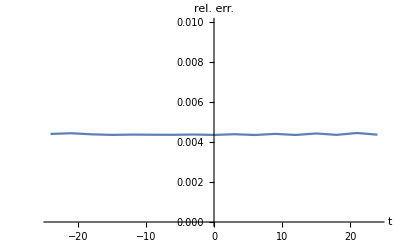

c:/temp/aa/norm_0_3_relerr.pdf

```mathematica
r1abs=Table[{rese3[[n,1]],Abs[rese3[[n,2]] -res3[[n,2]] ]/rese3[[n,2]]},{n,1,Length[rese3]}]
ListPlot[{r1abs},Joined->True,AxesLabel->{"t","rel. err."},PlotRange->{0,0.01}]
Export["c:/temp/aa/norm_0_3_relerr.pdf", %]
```

```mathematica
(* normal distribution *)
mean=-10.;
data={m->mean, s->1.5};
fs2[v_]:= Exp[-v*m+v^2 *s/2]/.data
rese15=Table[{T,PDF[NormalDistribution[m,Sqrt[s]]/.data,T]//N},{T,-24,24,3}]
res15=Table[{T,DSILTopt[fs2, T,30,-1000,1000]},{T,-24,24,3}]
```

{{-24,1.37708×10^-29},{-21,9.91563×10^-19},{-18,1.76976×10^-10},{-15,0.0000782968},{-12,0.0858628},{-9,0.233399},{-6,0.00157263},{-3,2.62656×10^-8},{0,1.08738×10^-15},{3,1.11586×10^-25},{6,2.83837×10^-38},{9,1.78962×10^-53},{12,2.79697×10^-71},{15,1.08355×10^-91},{18,1.04049×10^-114},{21,2.47665×10^-140},{24,1.46125×10^-168}}

{{-24,1.38316×10^-29},{-21,9.95913×10^-19},{-18,1.7777×10^-10},{-15,0.0000786397},{-12,0.0862491},{-9,0.234422},{-6,0.00157956},{-3,2.63815×10^-8},{0,1.0922×10^-15},{3,1.12076×10^-25},{6,2.85105×10^-38},{9,1.79747×10^-53},{12,2.80923×10^-71},{15,1.08836×10^-91},{18,1.04507×10^-114},{21,2.4876×10^-140},{24,1.46771×10^-168}}

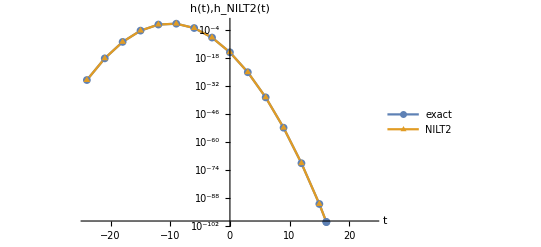

c:/temp/aa/norm_10_15.pdf

```mathematica
ListLogPlot[{rese15,res15},Joined->True,PlotRange->{10^-100,10^0},PlotMarkers->{{●,8},{▲,8}},PlotLegends->Placed[{"exact","NILT2"},{0.85,0.85}],AxesLabel->{"t","h(t),h_NILT2(t)"}]
Export["c:/temp/aa/norm_10_15.pdf", %]
```

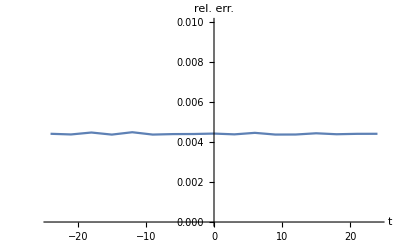

c:/temp/aa/norm_10_15_relerr.pdf

```mathematica
r1abs=Table[{rese15[[n,1]],Abs[rese15[[n,2]] -res15[[n,2]] ]/rese15[[n,2]]},{n,1,Length[rese15]}]
ListPlot[{r1abs},Joined->True,AxesLabel->{"t","rel. err."},PlotRange->{0,0.01}]
Export["c:/temp/aa/norm_10_15_relerr.pdf", %]
```

```mathematica
ft3[t_]:=ⅇ^(-Abs[t]^3)
ft2[t_]:=ⅇ^(-Abs[t]^2)
fs3[s_]:=1/18 (4 3^(2/3) π (AiryBi[-s/3^(1/3)]+AiryBi[s/3^(1/3)])+3 s^2 HypergeometricPFQ[{1},{4/3,5/3},-s^3/27]+3 s^2 HypergeometricPFQ[{1},{4/3,5/3},s^3/27])
```

```mathematica
resef3=Table[{T,ft3[T]},{T,-5,5,0.5}]//N;
resf3r2=Table[{T,DSILToptRefined[fs3 ,T,30,-1000,1000,"cme",200]},{T,-5,5,0.5}]//N;
resf3=Table[{resf3r2[[i,1]],resf3r2[[i,2,2]]},{i,Length[resf3r2]}]
resf3r=Table[{resf3r2[[i,1]],resf3r2[[i,2,1]]},{i,Length[resf3r2]}]
```

{{-5.,5.6747×10^-55},{-4.5,2.85921×10^-40},{-4.,1.69142×10^-28},{-3.5,2.48699×10^-19},{-3.,1.92414×10^-12},{-2.5,1.65826×10^-7},{-2.,0.000337022},{-1.5,0.0341954},{-1.,0.366698},{-0.5,0.879845},{0.,0.999679},{0.5,0.878815},{1.,0.363777},{1.5,0.0333856},{2.,0.000322831},{2.5,1.55047×10^-7},{3.,1.74667×10^-12},{3.5,2.18013×10^-19},{4.,1.42414×10^-28},{4.5,2.29991×10^-40},{5.,4.33743×10^-55}}

{{-5.,5.09368×10^-55},{-4.5,2.62636×10^-40},{-4.,1.58561×10^-28},{-3.5,2.37283×10^-19},{-3.,1.86338×10^-12},{-2.5,1.62559×10^-7},{-2.,0.000333528},{-1.5,0.0340937},{-1.,0.366505},{-0.5,0.879011},{0.,0.999679},{0.5,0.880507},{1.,0.375124},{1.5,0.0346623},{2.,0.000335748},{2.5,1.62781×10^-7},{3.,1.8635×10^-12},{3.5,2.37284×10^-19},{4.,1.58559×10^-28},{4.5,2.62634×10^-40},{5.,5.09363×10^-55}}

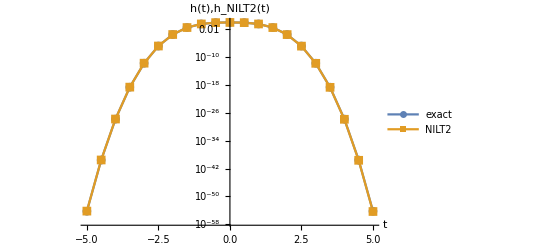

c:/temp/aa/f3_log.pdf

```mathematica
ListLogPlot[{resef3,resf3},Joined->True,PlotMarkers->Automatic,PlotLegends->Placed[{"exact","NILT2"},{0.8,0.15}],AxesLabel->{"t","h(t),h_NILT2(t)"},PlotRange->All]
Export["c:/temp/aa/f3_log.pdf", %]
```

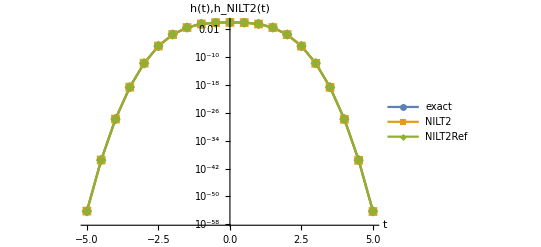

c:/temp/aa/f3_log_r.pdf

```mathematica
ListLogPlot[{resef3,resf3,resf3r},Joined->True,PlotRange->All,PlotMarkers->Automatic,PlotLegends->Placed[{"exact","NILT2","NILT2Ref"},{0.8,0.15}],AxesLabel->{"t","h(t),h_NILT2(t)"}]
Export["c:/temp/aa/f3_log_r.pdf", %]
```

```mathematica
r1abs=Table[{resef3[[n,1]],Abs[resef3[[n,2]] -resf3[[n,2]] ]/resef3[[n,2]]},{n,1,Length[resef3]}]
r1rabs=Table[{resef3[[n,1]],Abs[resef3[[n,2]] -resf3r[[n,2]] ]/resef3[[n,2]]},{n,1,Length[resef3]}]
```

{{-5.,0.0983807},{-4.5,0.0748085},{-4.,0.0546251},{-3.5,0.0376474},{-3.,0.0237346},{-2.5,0.0127518},{-2.,0.00464934},{-1.5,0.000665351},{-1.,0.0032126},{-0.5,0.00300457},{0.,0.000320643},{0.5,0.00417239},{1.,0.0111529},{1.5,0.0243292},{2.,0.0376555},{2.5,0.0530747},{3.,0.070689},{3.5,0.0903818},{4.,0.11203},{4.5,0.135438},{5.,0.160458}}

{{-5.,0.0140787},{-4.5,0.0127229},{-4.,0.0113486},{-3.5,0.00998391},{-3.,0.00859187},{-2.5,0.00719831},{-2.,0.00576754},{-1.5,0.00363686},{-1.,0.00373646},{-0.5,0.00395022},{0.,0.000320643},{0.5,0.00225431},{1.,0.0196934},{1.5,0.0129808},{2.,0.000849709},{2.5,0.00584036},{3.,0.00852548},{3.5,0.00998096},{4.,0.0113582},{4.5,0.0127306},{5.,0.0140896}}

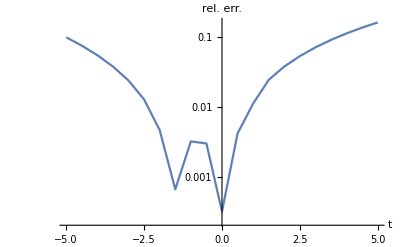

c:/temp/aa/f3_relerr.pdf

```mathematica
ListLogPlot[{r1abs},Joined->True,AxesLabel->{"t","rel. err."},PlotRange->All,Ticks->{Automatic,{0.001,0.002,0.005,0.01,0.02,0.05,0.1 }}]
Export["c:/temp/aa/f3_relerr.pdf", %]
```

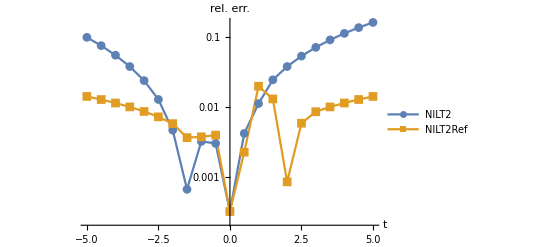

c:/temp/aa/f3_relerr_r.pdf

```mathematica
ListLogPlot[{r1abs,r1rabs},Joined->True,AxesLabel->{"t","rel. err."},PlotLegends->Placed[{"NILT2","NILT2Ref"},{0.85,0.15}],PlotRange->All,PlotMarkers->Automatic,Ticks->{Automatic,{0.001,0.002,0.005,0.01,0.02,0.05,0.1 }}]
Export["c:/temp/aa/f3_relerr_r.pdf", %]
```

2/3 ⅇ^(-5/11 (-15+t)^2) √(5/(11 π))+1/6 ⅇ^(-5/12 (-1+t)^2) √(5/(3 π))

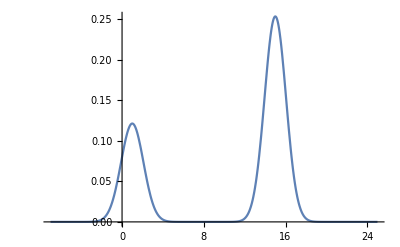

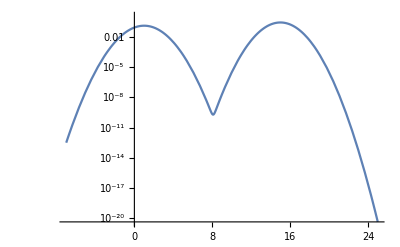

```mathematica
(* mixtures of normal  *)
p=1/3;
data1={m->1, s->12/10};
fs1[v_]:= Exp[-v*m+v^2 *s/2]/.data1
data2={m->15, s->11/10};
fs2[v_]:= Exp[-v*m+v^2 *s/2]/.data2
fs[v_]:= p fs1[v]+ (1-p)fs2[v]
ft[t_]=p PDF[NormalDistribution[m,Sqrt[s]]/.data1,t]+(1-p)PDF[NormalDistribution[m,Sqrt[s]]/.data2,t]
Plot[ft[t],{t,-7,25},PlotRange->All]
LogPlot[ft[t],{t,-7,25}]
```

```mathematica
T=4;
ft[T]//N
DSILTopt[fs, T,30,-1000,1000,"cme",100]//N
res=Table[{hshift,DSILThshift[fs, T,30,-1000,1000,hshift,"cme",100]},{hshift,5,40,5}];
%//N 
DSILToptRefined[fs, T,30,-1000,1000,"cme",150]//N
Clear[T]
```

0.00285492

T=4, m0=1., m1=10.3333, m2=151.466, cv=6.68507, scv=44.6902, Hshift=26.7403

The number of NILT calls in NILTopt: 18, {θmin,θmax,θopt}={-1000.,1000.,-36.6413}

0.00304146

{{5.,0.0201557},{10.,0.00316929},{15.,0.00302365},{20.,0.00302668},{25.,0.00303858},{30.,0.00304499},{35.,0.00304864},{40.,0.00333323}}

{0.0179333,0.00304146}

```mathematica
resem1=Table[{T,ft[T]//N},{T,-7,25,1}]//N
(* resm1=Table[{T,DSILTopt[fs, T,30,-1000,1000,"cme",100]},{T,-7,25,1}]//N *)
resm1r2=Table[{T,DSILToptRefined[fs, T,30,-1000,1000,"cme",100]},{T,-7,25,1}]//N;
resm1=Table[{resm1r2[[i,1]],resm1r2[[i,2,2]]},{i,Length[resm1r2]}]
resm1r=Table[{resm1r2[[i,1]],resm1r2[[i,2,1]]},{i,Length[resm1r2]}]
```

{{-7.,3.18429×10^-13},{-6.,1.6495×10^-10},{-5.,3.71348×10^-8},{-4.,3.63327×10^-6},{-3.,0.00015449},{-2.,0.00285492},{-1.,0.0229284},{0.,0.080028},{1.,0.121394},{2.,0.080028},{3.,0.0229284},{4.,0.00285492},{5.,0.00015449},{6.,3.63327×10^-6},{7.,3.71348×10^-8},{8.,2.18802×10^-10},{9.,1.98378×10^-8},{10.,2.94414×10^-6},{11.,0.000176042},{12.,0.00424095},{13.,0.041162},{14.,0.160959},{15.,0.253584},{16.,0.160959},{17.,0.041162},{18.,0.00424095},{19.,0.000176042},{20.,2.94414×10^-6},{21.,1.98374×10^-8},{22.,5.38518×10^-11},{23.,5.88981×10^-14},{24.,2.59531×10^-17},{25.,4.60749×10^-21}}

{{-7.,2.8192×10^-13},{-6.,1.46039×10^-10},{-5.,3.28772×10^-8},{-4.,3.21672×10^-6},{-3.,0.000136779},{-2.,0.0025276},{-1.,0.0202997},{0.,0.0708526},{1.,0.107477},{2.,0.0708535},{3.,0.0207529},{4.,0.00304146},{5.,0.00023873},{6.,0.0000120268},{7.,3.38431×10^-6},{8.,7.73246×10^-6},{9.,0.00002218},{10.,0.0000809202},{11.,0.000724565},{12.,0.00737516},{13.,0.0451046},{14.,0.14465},{15.,0.222352},{16.,0.141134},{17.,0.0360923},{18.,0.00371859},{19.,0.000154359},{20.,2.58151×10^-6},{21.,1.73941×10^-8},{22.,4.72193×10^-11},{23.,5.16435×10^-14},{24.,2.27564×10^-17},{25.,4.03998×10^-21}}

{{-7.,3.17889×10^-13},{-6.,1.64664×10^-10},{-5.,3.70703×10^-8},{-4.,3.62721×10^-6},{-3.,0.000154222},{-2.,0.00284997},{-1.,0.02289},{0.,0.0798891},{1.,0.121191},{2.,0.079998},{3.,0.0261789},{4.,0.0179333},{5.,0.00837352},{6.,0.0000120268},{7.,3.38431×10^-6},{8.,7.73246×10^-6},{9.,0.00002218},{10.,0.0000809202},{11.,0.000724565},{12.,0.0054977},{13.,0.0480526},{14.,0.171034},{15.,0.260363},{16.,0.162016},{17.,0.0410975},{18.,0.00423183},{19.,0.000175675},{20.,2.93782×10^-6},{21.,1.97952×10^-8},{22.,5.37354×10^-11},{23.,5.87711×10^-14},{24.,2.58974×10^-17},{25.,4.59753×10^-21}}

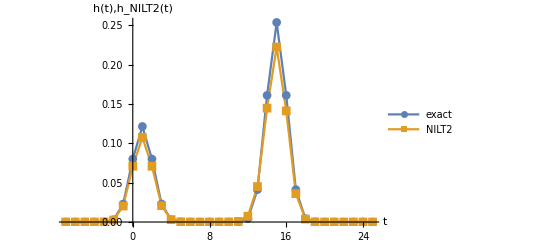

c:/temp/aa/mixnorm_1_lin.pdf

```mathematica
ListPlot[{resem1,resm1},Joined->True,PlotRange->All,PlotMarkers->Automatic,PlotLegends->Placed[{"exact","NILT2","NILT2Ref"},{0.85,0.8}],AxesLabel->{"t","h(t),h_NILT2(t)"}]
Export["c:/temp/aa/mixnorm_1_lin.pdf", %]
```

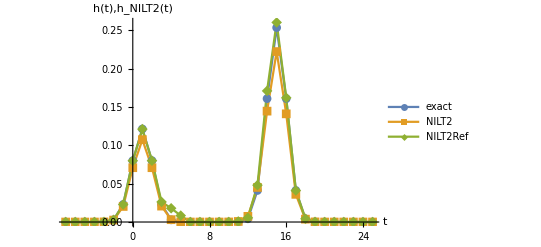

c:/temp/aa/mixnorm_1_lin_r.pdf

```mathematica
ListPlot[{resem1,resm1,resm1r},Joined->True,PlotRange->All,PlotMarkers->Automatic,PlotLegends->Placed[{"exact","NILT2","NILT2Ref"},{0.85,0.8}],AxesLabel->{"t","h(t),h_NILT2(t)"}]
Export["c:/temp/aa/mixnorm_1_lin_r.pdf", %]
```

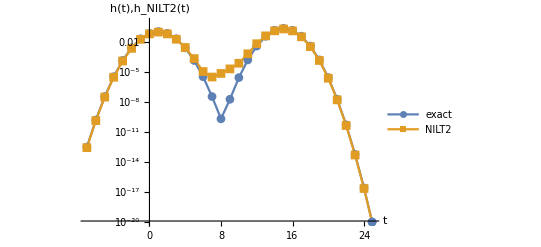

c:/temp/aa/mixnorm_1_log.pdf

```mathematica
ListLogPlot[{resem1,resm1},Joined->True,PlotRange->{10^-20,10^0},PlotMarkers->Automatic,PlotLegends->Placed[{"exact","NILT2"},{0.8,0.15}],AxesLabel->{"t","h(t),h_NILT2(t)"}]
Export["c:/temp/aa/mixnorm_1_log.pdf", %]
```

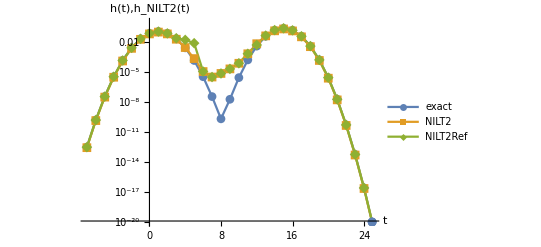

c:/temp/aa/mixnorm_1_log_r.pdf

```mathematica
ListLogPlot[{resem1,resm1,resm1r},Joined->True,PlotRange->{10^-20,10^0},PlotMarkers->Automatic(*{{●,8},{▲,8},{▲,8}}*),PlotLegends->Placed[{"exact","NILT2","NILT2Ref"},{0.8,0.15}],AxesLabel->{"t","h(t),h_NILT2(t)"}]
Export["c:/temp/aa/mixnorm_1_log_r.pdf", %]
```

```mathematica
r1abs=Table[{resem1[[n,1]],Abs[resem1[[n,2]] -resm1[[n,2]] ]/resem1[[n,2]]},{n,1,Length[resem1]}]
r1rabs=Table[{resem1[[n,1]],Abs[resem1[[n,2]] -resm1r[[n,2]] ]/resem1[[n,2]]},{n,1,Length[resem1]}]
```

{{-7,0.114652},{-6,0.11465},{-5,0.114652},{-4,0.114649},{-3,0.114644},{-2,0.114652},{-1,0.114649},{0,0.114652},{1,0.114647},{2,0.114641},{3,0.0948827},{4,0.0653406},{5,0.545276},{6,2.31019},{7,90.1357},{8,35339.},{9,1117.07},{10,26.4852},{11,3.11586},{12,0.739035},{13,0.0957826},{14,0.101324},{15,0.123165},{16,0.123169},{17,0.123164},{18,0.123172},{19,0.123171},{20,0.123169},{21,0.12317},{22,0.123161},{23,0.123171},{24,0.12317},{25,0.123171}}

{{-7,0.00169464},{-6,0.00173214},{-5,0.00173763},{-4,0.00166704},{-3,0.00173686},{-2,0.00173512},{-1,0.00167639},{0,0.00173557},{1,0.00167457},{2,0.000374808},{3,0.141767},{4,5.28153},{5,53.2009},{6,2.31019},{7,90.1357},{8,35339.},{9,1117.07},{10,26.4852},{11,3.11586},{12,0.296336},{13,0.167403},{14,0.0625921},{15,0.0267304},{16,0.0065645},{17,0.00156579},{18,0.00215149},{19,0.00208507},{20,0.00214527},{21,0.00212904},{22,0.00216097},{23,0.00215615},{24,0.00214522},{25,0.00216212}}

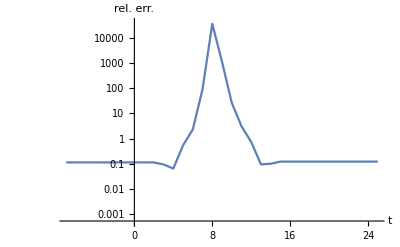

c:/temp/aa/mixnorm_1_relerr.pdf

```mathematica
ListLogPlot[{r1abs},Joined->True,AxesLabel->{"t","rel. err."},PlotRange->{0.0005, 40000},Ticks->{Automatic,{0.01,1,10^2,10^4}}]
Export["c:/temp/aa/mixnorm_1_relerr.pdf", %]
```

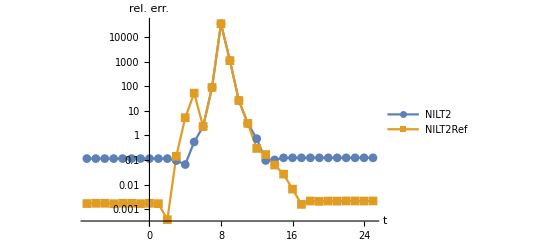

c:/temp/aa/mixnorm_1_relerr_r.pdf

```mathematica
ListLogPlot[{r1abs,r1rabs},Joined->True,AxesLabel->{"t","rel. err."},PlotLegends->Placed[{"NILT2","NILT2Ref"},{0.8,0.65}],PlotRange->{0.0003, 40000},PlotMarkers ->Automatic, Ticks->{Automatic,{0.001,0.01,0.1,1,10,100,100,1000,10000}}]
Export["c:/temp/aa/mixnorm_1_relerr_r.pdf", %]
```

```mathematica
resem1=Table[{T,ft[T]//N},{T,-7,25,1}]
resm160=Table[{T,DSILTopt[fs, T,60,-1000,1000]},{T,-7,25,1}]
```

{{-7,3.18429×10^-13},{-6,1.6495×10^-10},{-5,3.71348×10^-8},{-4,3.63327×10^-6},{-3,0.00015449},{-2,0.00285492},{-1,0.0229284},{0,0.080028},{1,0.121394},{2,0.080028},{3,0.0229284},{4,0.00285492},{5,0.00015449},{6,3.63327×10^-6},{7,3.71348×10^-8},{8,2.18802×10^-10},{9,1.98378×10^-8},{10,2.94414×10^-6},{11,0.000176042},{12,0.00424095},{13,0.041162},{14,0.160959},{15,0.253584},{16,0.160959},{17,0.041162},{18,0.00424095},{19,0.000176042},{20,2.94414×10^-6},{21,1.98374×10^-8},{22,5.38518×10^-11},{23,5.88981×10^-14},{24,2.59531×10^-17},{25,4.60749×10^-21}}

{{-7,3.08993×10^-13},{-6,1.60062×10^-10},{-5,3.60344×10^-8},{-4,3.52562×10^-6},{-3,0.000149913},{-2,0.00277032},{-1,0.022249},{0,0.0776566},{1,0.117797},{2,0.0776567},{3,0.0223031},{4,0.00287231},{5,0.00017019},{6,4.79312×10^-6},{7,8.04366×10^-8},{8,5.04641×10^-8},{9,4.92671×10^-7},{10,8.87912×10^-6},{11,0.000265088},{12,0.00492279},{13,0.0420888},{14,0.156566},{15,0.245433},{16,0.155785},{17,0.0398387},{18,0.00410462},{19,0.000170383},{20,2.8495×10^-6},{21,1.91997×10^-8},{22,5.21206×10^-11},{23,5.70047×10^-14},{24,2.51188×10^-17},{25,4.45938×10^-21}}

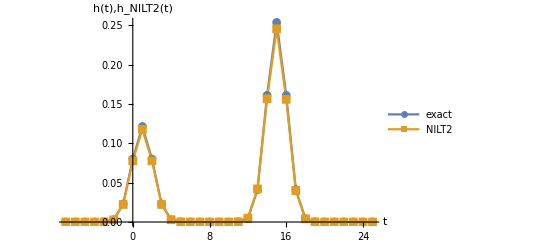

c:/temp/aa/mixnorm_1_60_lin.pdf

```mathematica
ListPlot[{resem1,resm160},Joined->True,PlotRange->All,PlotMarkers->Automatic,PlotLegends->Placed[{"exact","NILT2"},{0.85,0.65}],AxesLabel->{"t","h(t),h_NILT2(t)"}]
Export["c:/temp/aa/mixnorm_1_60_lin.pdf", %]
```

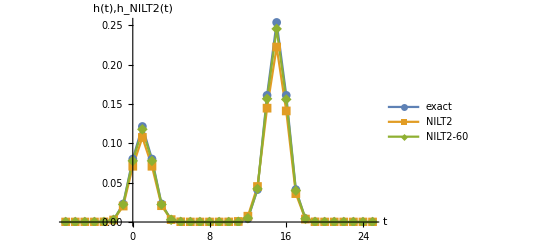

c:/temp/aa/mixnorm_1_30-60_lin.pdf

```mathematica
ListPlot[{resem1,resm1,resm160},Joined->True,PlotRange->All,PlotMarkers->Automatic,PlotLegends->Placed[{"exact","NILT2","NILT2-60"},{0.85,0.65}],AxesLabel->{"t","h(t),h_NILT2(t)"}]
Export["c:/temp/aa/mixnorm_1_30-60_lin.pdf", %]
```

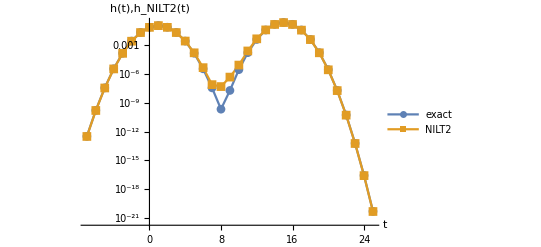

c:/temp/aa/mixnorm_1_60_log.pdf

```mathematica
ListLogPlot[{resem1,resm160},Joined->True,PlotRange->All,PlotMarkers->Automatic,PlotLegends->Placed[{"exact","NILT2"},{0.8,0.15}],AxesLabel->{"t","h(t),h_NILT2(t)"}]
Export["c:/temp/aa/mixnorm_1_60_log.pdf", %]
```

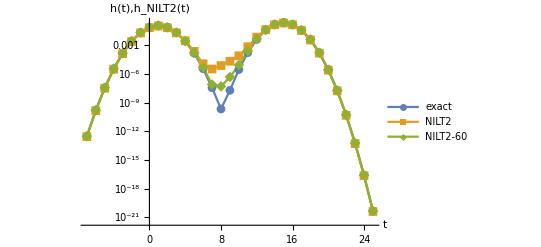

c:/temp/aa/mixnorm_1_30-60_log.pdf

```mathematica
ListLogPlot[{resem1,resm1,resm160},Joined->True,PlotRange->All,PlotMarkers->Automatic,PlotLegends->Placed[{"exact","NILT2","NILT2-60"},{0.85,0.15}],AxesLabel->{"t","h(t),h_NILT2(t)"}]
Export["c:/temp/aa/mixnorm_1_30-60_log.pdf", %]
```

```mathematica
r160abs=Table[{resem1[[n,1]],Abs[resem1[[n,2]] -resm160[[n,2]] ]/resem1[[n,2]]},{n,1,Length[resem1]}]
```

{{-7,0.0296324},{-6,0.0296316},{-5,0.0296322},{-4,0.0296295},{-3,0.0296317},{-2,0.0296322},{-1,0.029632},{0,0.0296319},{1,0.0296289},{2,0.0296319},{3,0.0272725},{4,0.00609173},{5,0.101624},{6,0.319233},{7,1.16607},{8,229.638},{9,23.835},{10,2.01587},{11,0.50582},{12,0.160775},{13,0.0225174},{14,0.0272945},{15,0.0321433},{16,0.0321469},{17,0.0321466},{18,0.032147},{19,0.0321471},{20,0.0321446},{21,0.0321465},{22,0.0321461},{23,0.0321472},{24,0.0321472},{25,0.0321454}}

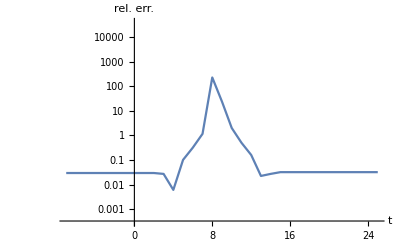

c:/temp/aa/mixnorm_1_60_relerr.pdf

```mathematica
ListLogPlot[{r160abs},Joined->True,AxesLabel->{"t","rel. err."},PlotRange->{0.0003, 40000},Ticks->{Automatic,{0.001,0.01,0.1,1,10,100,100,1000,10000}}]
Export["c:/temp/aa/mixnorm_1_60_relerr.pdf", %]
```

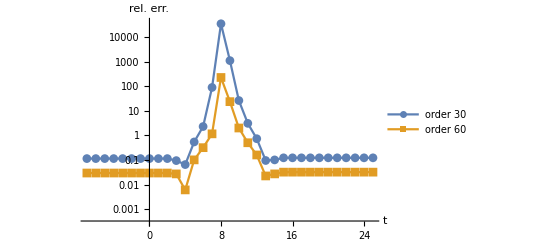

c:/temp/aa/mixnorm_1_30-60_relerr.pdf

```mathematica
ListLogPlot[{r1abs,r160abs},Joined->True,AxesLabel->{"t","rel. err."},PlotLegends->Placed[{"order 30","order 60"},{0.8,0.65}],PlotRange->{0.0003, 40000},PlotMarkers->Automatic,Ticks->{Automatic,{0.001,0.01,0.1,1,10,100,100,1000,10000}}]
Export["c:/temp/aa/mixnorm_1_30-60_relerr.pdf", %]
```

2/3 ⅇ^(-5/11 (-5+t)^2) √(5/(11 π))+1/6 ⅇ^(-5/12 (-1+t)^2) √(5/(3 π))

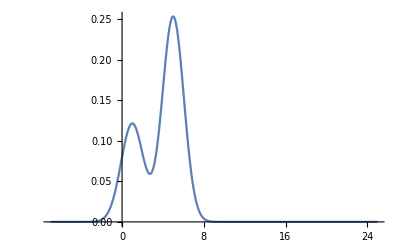

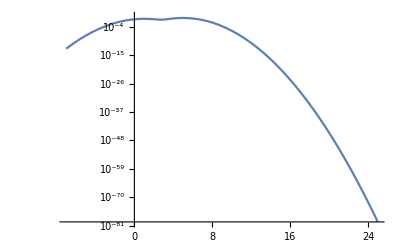

```mathematica
(* mixtures of normal  *)
p=1/3;
data1={m->1, s->12/10};
fs1[v_]:= Exp[-v*m+v^2 *s/2]/.data1
data2={m->5, s->11/10};
fs2[v_]:= Exp[-v*m+v^2 *s/2]/.data2
fs[v_]:= p fs1[v]+ (1-p)fs2[v]
ft[t_]=p PDF[NormalDistribution[m,Sqrt[s]]/.data1,t]+(1-p)PDF[NormalDistribution[m,Sqrt[s]]/.data2,t]
Plot[ft[t],{t,-7,25},PlotRange->All]
LogPlot[ft[t],{t,-7,25}]
```

```mathematica
resem2=Table[{T,ft[T]//N},{T,-7,15,0.5}]
(* resm2=Table[{T,DSILTopt[fs, T,30,-1000,1000]},{T,-7,15,0.5}] *)
resm2r2=Table[{T,DSILToptRefined[fs, T,30,-1000,1000,"cme",100]},{T,-7,15,0.5}]//N;
resm2=Table[{resm2r2[[i,1]],resm2r2[[i,2,2]]},{i,Length[resm2r2]}]
resm2r=Table[{resm2r2[[i,1]],resm2r2[[i,2,1]]},{i,Length[resm2r2]}]
```

{{-7.,3.18429×10^-13},{-6.5,8.04306×10^-12},{-6.,1.6495×10^-10},{-5.5,2.74667×10^-9},{-5.,3.71348×10^-8},{-4.5,4.07641×10^-7},{-4.,3.63327×10^-6},{-3.5,0.0000262929},{-3.,0.00015449},{-2.5,0.000737033},{-2.,0.00285492},{-1.5,0.0089789},{-1.,0.0229284},{-0.5,0.0475389},{0.,0.080031},{0.5,0.109411},{1.,0.12157},{1.5,0.110353},{2.,0.084269},{2.5,0.0623411},{3.,0.0640904},{3.5,0.100171},{4.,0.163814},{4.5,0.227082},{5.,0.253739},{5.5,0.226371},{6.,0.160963},{6.5,0.0911926},{7.,0.041162},{7.5,0.0148024},{8.,0.00424095},{8.5,0.000968037},{9.,0.000176042},{9.5,0.0000255058},{10.,2.94414×10^-6},{10.5,2.70753×10^-7},{11.,1.98374×10^-8},{11.5,1.15796×10^-9},{12.,5.38518×10^-11},{12.5,1.99527×10^-12},{13.,5.88981×10^-14},{13.5,1.38515×10^-15},{14.,2.59531×10^-17},{14.5,3.87417×10^-19},{15.,4.60749×10^-21}}

{{-7.,3.13878×10^-13},{-6.5,7.92795×10^-12},{-6.,1.62585×10^-10},{-5.5,2.70721×10^-9},{-5.,3.66008×10^-8},{-4.5,4.01769×10^-7},{-4.,3.58083×10^-6},{-3.5,0.0000259132},{-3.,0.000152254},{-2.5,0.000726351},{-2.,0.00281346},{-1.5,0.00884829},{-1.,0.0225943},{-0.5,0.0468457},{0.,0.0788622},{0.5,0.107816},{1.,0.119835},{1.5,0.108982},{2.,0.0840199},{2.5,0.0639389},{3.,0.0662906},{3.5,0.10074},{4.,0.162467},{4.5,0.224111},{5.,0.249925},{5.5,0.222807},{6.,0.158395},{6.5,0.0897324},{7.,0.0405017},{7.5,0.0145646},{8.,0.00417271},{8.5,0.000952434},{9.,0.000173201},{9.5,0.0000250937},{10.,2.89646×10^-6},{10.5,2.66362×10^-7},{11.,1.95153×10^-8},{11.5,1.13914×10^-9},{12.,5.29749×10^-11},{12.5,1.96272×10^-12},{13.,5.79355×10^-14},{13.5,1.36248×10^-15},{14.,2.55278×10^-17},{14.5,3.81056×10^-19},{15.,4.53173×10^-21}}

{{-7.,3.19595×10^-13},{-6.5,8.07196×10^-12},{-6.,1.65546×10^-10},{-5.5,2.75667×10^-9},{-5.,3.72672×10^-8},{-4.5,4.09098×10^-7},{-4.,3.64627×10^-6},{-3.5,0.0000263867},{-3.,0.000155054},{-2.5,0.00073969},{-2.,0.0028659},{-1.5,0.0090109},{-1.,0.0230103},{-0.5,0.0477101},{0.,0.0803234},{0.5,0.109837},{1.,0.122084},{1.5,0.110424},{2.,0.0840199},{2.5,0.0639389},{3.,0.0662906},{3.5,0.10074},{4.,0.172668},{4.5,0.238752},{5.,0.264386},{5.5,0.233828},{6.,0.164974},{6.5,0.0928218},{7.,0.0416619},{7.5,0.0149166},{8.,0.00426146},{8.5,0.000971747},{9.,0.000176669},{9.5,0.0000255953},{10.,2.95444×10^-6},{10.5,2.71702×10^-7},{11.,1.99068×10^-8},{11.5,1.16203×10^-9},{12.,5.404×10^-11},{12.5,2.00232×10^-12},{13.,5.91042×10^-14},{13.5,1.39007×10^-15},{14.,2.60463×10^-17},{14.5,3.88804×10^-19},{15.,4.62392×10^-21}}

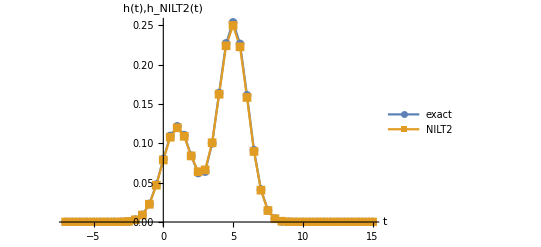

c:/temp/aa/mixnorm_2_lin.pdf

```mathematica
ListPlot[{resem2,resm2},Joined->True,PlotRange->All,PlotMarkers->Automatic,PlotLegends->Placed[{"exact","NILT2"},{0.85,0.65}],AxesLabel->{"t","h(t),h_NILT2(t)"}]
Export["c:/temp/aa/mixnorm_2_lin.pdf", %]
```

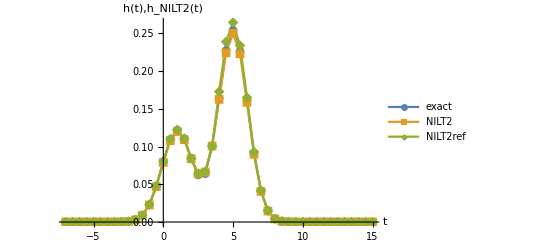

c:/temp/aa/mixnorm_2_lin_r.pdf

```mathematica
ListPlot[{resem2,resm2,resm2r},Joined->True,PlotRange->All,PlotMarkers->Automatic,PlotLegends->Placed[{"exact","NILT2","NILT2ref"},{0.85,0.65}],AxesLabel->{"t","h(t),h_NILT2(t)"}]
Export["c:/temp/aa/mixnorm_2_lin_r.pdf", %]
```

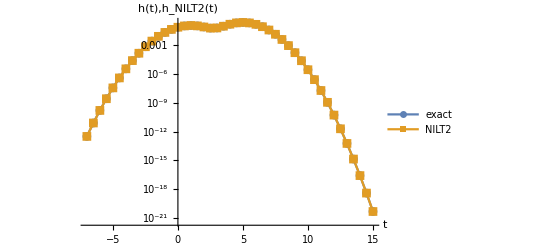

c:/temp/aa/mixnorm_2_log.pdf

```mathematica
ListLogPlot[{resm2,resm2},Joined->True,PlotRange->All,PlotMarkers->Automatic,PlotLegends->Placed[{"exact","NILT2"},{0.85,0.15}],AxesLabel->{"t","h(t),h_NILT2(t)"}]
Export["c:/temp/aa/mixnorm_2_log.pdf", %]
```

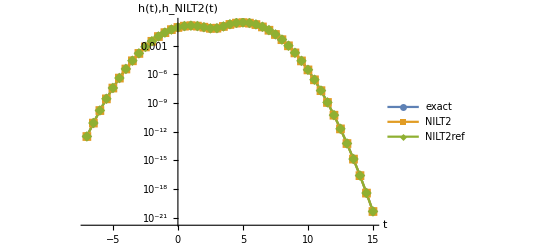

c:/temp/aa/mixnorm_2_log_r.pdf

```mathematica
ListLogPlot[{resem2,resm2,resm2r},Joined->True,PlotRange->All,PlotMarkers->Automatic,PlotLegends->Placed[{"exact","NILT2","NILT2ref"},{0.8,0.15}],AxesLabel->{"t","h(t),h_NILT2(t)"}]
Export["c:/temp/aa/mixnorm_2_log_r.pdf", %]
```

```mathematica
r1abs=Table[{resem2[[n,1]],Abs[resem2[[n,2]] -resm2[[n,2]] ]/resem2[[n,2]]},{n,1,Length[resem2]}]
r1rabs=Table[{resem2[[n,1]],Abs[resem2[[n,2]] -resm2r[[n,2]] ]/resem2[[n,2]]},{n,1,Length[resem2]}]
```

{{-7.,0.0142896},{-6.5,0.0143113},{-6.,0.0143405},{-5.5,0.0143633},{-5.,0.0143807},{-4.5,0.0144043},{-4.,0.0144321},{-3.5,0.0144407},{-3.,0.014479},{-2.5,0.0144934},{-2.,0.0145212},{-1.5,0.0145461},{-1.,0.0145709},{-0.5,0.0145826},{0.,0.0146037},{0.5,0.014573},{1.,0.0142711},{1.5,0.0124311},{2.,0.0029562},{2.5,0.0256302},{3.,0.0343296},{3.5,0.00567969},{4.,0.00822414},{4.5,0.0130827},{5.,0.0150299},{5.5,0.0157446},{6.,0.0159555},{6.5,0.0160118},{7.,0.0160409},{7.5,0.0160621},{8.,0.0160905},{8.5,0.0161176},{9.,0.0161403},{9.5,0.0161588},{10.,0.0161923},{10.5,0.0162173},{11.,0.0162379},{11.5,0.0162543},{12.,0.0162826},{12.5,0.016315},{13.,0.016343},{13.5,0.0163667},{14.,0.0163869},{14.5,0.0164172},{15.,0.0164431}}

{{-7.,0.00366275},{-6.5,0.00359273},{-6.,0.00361424},{-5.5,0.00364208},{-5.,0.00356564},{-4.5,0.00357335},{-4.,0.00357858},{-3.5,0.00356875},{-3.,0.00364517},{-2.5,0.00360526},{-2.,0.00384778},{-1.5,0.00356466},{-1.,0.00357217},{-0.5,0.00360065},{0.,0.00365346},{0.5,0.00389941},{1.,0.00422554},{1.5,0.000638732},{2.,0.0029562},{2.5,0.0256302},{3.,0.0343296},{3.5,0.00567969},{4.,0.0540483},{4.5,0.0513908},{5.,0.0419619},{5.5,0.0329394},{6.,0.0249177},{6.5,0.017865},{7.,0.0121453},{7.5,0.00771376},{8.,0.00483537},{8.5,0.00383301},{9.,0.00356017},{9.5,0.00350851},{10.,0.0035001},{10.5,0.00350443},{11.,0.00349466},{11.5,0.00351563},{12.,0.00349511},{12.5,0.00353193},{13.,0.00350002},{13.5,0.00355321},{14.,0.00359021},{14.5,0.00357958},{15.,0.00356571}}

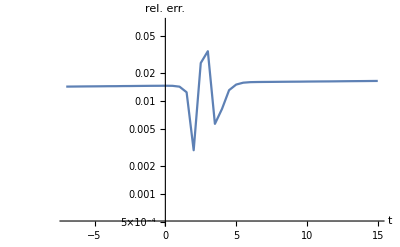

c:/temp/aa/mixnorm_2_relerr.pdf

```mathematica
ListLogPlot[r1abs,Joined->True,AxesLabel->{"t","rel. err."},PlotRange->{0.0005, 0.07},Ticks->{Automatic,{0.001,0.002,0.005,0.01,0.02,0.05,0.1}}]
Export["c:/temp/aa/mixnorm_2_relerr.pdf", %]
```

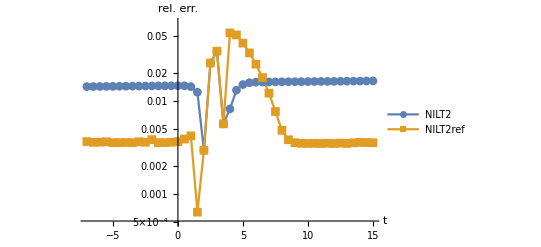

c:/temp/aa/mixnorm_2_relerr_r.pdf

```mathematica
ListLogPlot[{r1abs,r1rabs},Joined->True,AxesLabel->{"t","rel. err."},PlotLegends->Placed[{"NILT2","NILT2ref"},{0.8,0.15}],PlotRange->{0.0005, 0.07},PlotMarkers->{Automatic},Ticks->{Automatic,{0.001,0.002,0.005,0.01,0.02,0.05,0.1}}]
Export["c:/temp/aa/mixnorm_2_relerr_r.pdf", %]
```

```mathematica
(* one Markovian transition  *)
λ=1;
T=1;
data={m1->1, s1->20/10,m2->15, s2->11/10};
(* pdf, if there is a state transition from 1 to 2 at t *)
ftt[x_,t_]:=  PDF[NormalDistribution[m1 t+m2 (T-t),Sqrt[s1 t+s2 (T-t)]]/.data,x]
```

```mathematica
(* overall pdf for one step ctmc with rate λ *)
ft[x_]:=ⅇ^(-λ T) PDF[NormalDistribution[m1 T,Sqrt[s1 T]]/.data,x]+NIntegrate[λ ⅇ^(-λ t) ftt[x,t],{t,0,T}]
```

```mathematica
res=Table[{x,ft[x]},{x,-6,20,0.5}]
```

{{-6.,5.05473×10^-7},{-5.5,2.7364×10^-6},{-5.,0.0000130758},{-4.5,0.0000551542},{-4.,0.000205373},{-3.5,0.000675148},{-3.,0.00195972},{-2.5,0.00502344},{-2.,0.0113741},{-1.5,0.0227558},{-1.,0.0402479},{-0.5,0.0629809},{0.,0.087303},{0.5,0.107423},{1.,0.117741},{1.5,0.115661},{2.,0.10295},{2.5,0.0846581},{3.,0.0664381},{3.5,0.0521498},{4.,0.0430414},{4.5,0.0384115},{5.,0.0367989},{5.5,0.0368671},{6.,0.0377394},{6.5,0.0389591},{7.,0.0403305},{7.5,0.0417832},{8.,0.0432966},{8.5,0.0448668},{9.,0.0464943},{9.5,0.0481808},{10.,0.0499285},{10.5,0.0517392},{11.,0.0536122},{11.5,0.0555339},{12.,0.0574366},{12.5,0.0590879},{13.,0.059894},{13.5,0.0587564},{14.,0.054331},{14.5,0.0459095},{15.,0.0343933},{15.5,0.0222608},{16.,0.0121993},{16.5,0.00557617},{17.,0.00210285},{17.5,0.000649114},{18.,0.000163073},{18.5,0.0000332015},{19.,5.46099×10^-6},{19.5,7.23911×10^-7},{20.,7.71963×10^-8}}

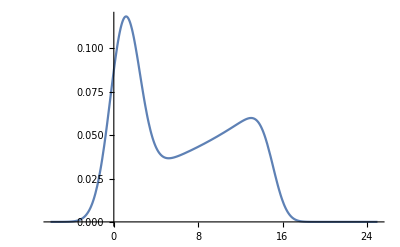

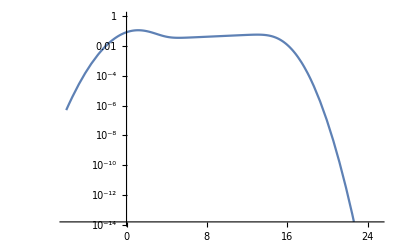

```mathematica
Plot[{ft[x]},{x,-6,20}]
LogPlot[{ft[x]},{x,-6,20}]
```

```mathematica
(* 3x3 MFM *)
Q={{-1,1},{0,-0}};
R={{m1,0},{0,m2}}/.data;
S={{s1,0},{0,s2}}/.data;
Clear[H]
H[v_]:=MatrixExp[Q-v*R+v^2 *S/2][[1,1]]+MatrixExp[Q-v*R+v^2 *S/2][[1,2]]
```

```mathematica
ft[1]//N
DSILToptRefined[H,1,30,-100,100,"cme",100]//N
```

0.117741

{0.117725,0.112869}

```mathematica
(* reslt=Table[{x,DSILTopt[H,x,30,-10000,10000]},{x,-6,20,0.5}] *)
resltr2=Table[{x,DSILToptRefined[H,x,30,-10000,10000,"cme",100]},{x,-6,20,0.5}]//N;
reslt=Table[{resltr2[[i,1]],resltr2[[i,2,2]]},{i,Length[resltr2]}]
resltr=Table[{resltr2[[i,1]],resltr2[[i,2,1]]},{i,Length[resltr2]}]
```

{{-6.,4.81692×10^-7},{-5.5,2.60773×10^-6},{-5.,0.0000124613},{-4.5,0.0000525635},{-4.,0.000195735},{-3.5,0.000643489},{-3.,0.00186796},{-2.5,0.00478868},{-2.,0.0108439},{-1.5,0.0216993},{-1.,0.0383907},{-0.5,0.0601034},{0.,0.0833795},{0.5,0.102733},{1.,0.112869},{1.5,0.11135},{2.,0.0998708},{2.5,0.0831794},{3.,0.0664778},{3.5,0.0531906},{4.,0.0443819},{4.5,0.0395242},{5.,0.0375056},{5.5,0.0372372},{6.,0.0379086},{6.5,0.0390315},{7.,0.0403616},{7.5,0.0417981},{8.,0.0433051},{8.5,0.0448723},{9.,0.0464982},{9.5,0.0481835},{10.,0.0499297},{10.5,0.0517368},{11.,0.0535985},{11.5,0.0554838},{12.,0.0572838},{12.5,0.0586961},{13.,0.0590752},{13.5,0.0573739},{14.,0.0524468},{14.5,0.0438326},{15.,0.0325352},{15.5,0.0209085},{16.,0.0113983},{16.5,0.00519041},{17.,0.00195207},{17.5,0.000601392},{18.,0.000150869},{18.5,0.0000306839},{19.,5.04284×10^-6},{19.5,6.68072×10^-7},{20.,7.12078×10^-8}}

{{-6.,5.06428×10^-7},{-5.5,2.74139×10^-6},{-5.,0.0000131004},{-4.5,0.0000552539},{-4.,0.000205741},{-3.5,0.000676358},{-3.,0.00196317},{-2.5,0.0050323},{-2.,0.0113935},{-1.5,0.0227934},{-1.,0.0403121},{-0.5,0.063069},{0.,0.0874024},{0.5,0.107502},{1.,0.117723},{1.5,0.115471},{2.,0.102554},{2.5,0.0843169},{3.,0.0664778},{3.5,0.0531906},{4.,0.0443819},{4.5,0.0395242},{5.,0.0375056},{5.5,0.0372372},{6.,0.0379086},{6.5,0.0390315},{7.,0.0403616},{7.5,0.0417981},{8.,0.0433051},{8.5,0.0448723},{9.,0.0464982},{9.5,0.0481835},{10.,0.0499297},{10.5,0.0517368},{11.,0.0535985},{11.5,0.0554838},{12.,0.0572838},{12.5,0.0595359},{13.,0.0629475},{13.5,0.0613346},{14.,0.0563094},{14.5,0.0473491},{15.,0.0352952},{15.5,0.0227326},{16.,0.0124026},{16.5,0.00564719},{17.,0.00212299},{17.5,0.000653704},{18.,0.000163904},{18.5,0.0000333234},{19.,5.47533×10^-6},{19.5,7.25285×10^-7},{20.,7.73042×10^-8}}

```mathematica
resltr2x=Join[resltr2x, resltr2e]
reslt=Table[{resltr2x[[i,1]],resltr2x[[i,2,2]]},{i,Length[resltr2x]}]
resltr=Table[{resltr2x[[i,1]],resltr2x[[i,2,1]]},{i,Length[resltr2x]}]
```

{{-6.,4.81692×10^-7},{-5.5,2.60773×10^-6},{-5.,0.0000124613},{-4.5,0.0000525635},{-4.,0.000195735},{-3.5,0.000643489},{-3.,0.00186796},{-2.5,0.00478868},{-2.,0.0108439},{-1.5,0.0216993},{-1.,0.0383907},{-0.5,0.0601034},{0.,0.0833795},{0.5,0.102733},{1.,0.112869},{1.5,0.11135},{2.,0.0998708},{2.5,0.0831794},{3.,0.0664778},{3.5,0.0531906},{4.,0.0443819},{4.5,0.0395242},{5.,0.0375056},{5.5,0.0372372},{6.,0.0379086},{6.5,0.0390315},{7.,0.0403616},{7.5,0.0417981},{8.,0.0433051},{8.5,0.0448723},{9.,0.0464982},{9.5,0.0481835},{10.,0.0499297},{10.5,0.0517368},{11.,0.0535985},{11.5,0.0554838},{12.,0.0572838},{12.5,0.0586961},{13.,0.0590752},{13.5,0.0573739},{14.,0.0524468},{14.5,0.0438326},{15.,0.0325352},{15.5,0.0209085},{16.,0.0113983},{16.5,0.00519041},{17.,0.00195207},{17.5,0.000601392},{18.,0.000150869},{18.5,0.0000306839},{19.,5.04284×10^-6},{19.5,6.68072×10^-7},{20.,7.12078×10^-8},{20.5,6.09743×10^-9},{21.,4.18962×10^-10},{21.5,2.30781×10^-11},{22.,1.01835×10^-12},{22.5,3.59746×10^-14},{23.,1.01687×10^-15},{23.5,2.29896×10^-17},{24.,4.1556×10^-19},{24.5,6.00396×10^-21},{25.,6.93159×10^-23},{25.5,6.39328×10^-25},{26.,4.7101×10^-27},{26.5,2.77127×10^-29},{27.,1.302×10^-31},{27.5,4.884×10^-34},{28.,1.46261×10^-36},{28.5,3.49647×10^-39},{29.,6.67192×10^-42},{29.5,1.01617×10^-44},{30.,1.23522×10^-47}}

{{-6.,5.06428×10^-7},{-5.5,2.74139×10^-6},{-5.,0.0000131004},{-4.5,0.0000552539},{-4.,0.000205741},{-3.5,0.000676358},{-3.,0.00196317},{-2.5,0.0050323},{-2.,0.0113935},{-1.5,0.0227934},{-1.,0.0403121},{-0.5,0.063069},{0.,0.0874024},{0.5,0.107502},{1.,0.117723},{1.5,0.115471},{2.,0.102554},{2.5,0.0843169},{3.,0.0664778},{3.5,0.0531906},{4.,0.0443819},{4.5,0.0395242},{5.,0.0375056},{5.5,0.0372372},{6.,0.0379086},{6.5,0.0390315},{7.,0.0403616},{7.5,0.0417981},{8.,0.0433051},{8.5,0.0448723},{9.,0.0464982},{9.5,0.0481835},{10.,0.0499297},{10.5,0.0517368},{11.,0.0535985},{11.5,0.0554838},{12.,0.0572838},{12.5,0.0595359},{13.,0.0629475},{13.5,0.0613346},{14.,0.0563094},{14.5,0.0473491},{15.,0.0352952},{15.5,0.0227326},{16.,0.0124026},{16.5,0.00564719},{17.,0.00212299},{17.5,0.000653704},{18.,0.000163904},{18.5,0.0000333234},{19.,5.47533×10^-6},{19.5,7.25285×10^-7},{20.,7.73042×10^-8},{20.5,6.61966×10^-9},{21.,4.54885×10^-10},{21.5,2.5058×10^-11},{22.,1.10578×10^-12},{22.5,3.90656×10^-14},{23.,1.10432×10^-15},{23.5,2.49691×10^-17},{24.,4.51359×10^-19},{24.5,6.52118×10^-21},{25.,7.52952×10^-23},{25.5,6.94469×10^-25},{26.,5.1163×10^-27},{26.5,3.01033×10^-29},{27.,1.41437×10^-31},{27.5,5.30548×10^-34},{28.,1.58883×10^-36},{28.5,3.7983×10^-39},{29.,7.2481×10^-42},{29.5,1.10394×10^-44},{30.,1.34183×10^-47}}

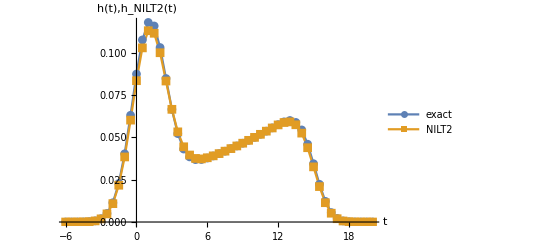

c:/temp/aa/mfm_lin.pdf

```mathematica
ListPlot[{res,reslt},Joined->True,PlotRange->All,PlotMarkers->Automatic,PlotLegends->Placed[{"exact","NILT2"},{0.85,0.85}],AxesLabel->{"t","h(t),h_NILT2(t)"}]
Export["c:/temp/aa/mfm_lin.pdf", %]
```

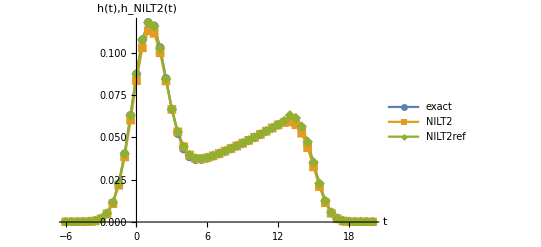

c:/temp/aa/mfm_lin_r.pdf

```mathematica
ListPlot[{res,reslt,resltr},Joined->True,PlotRange->All,PlotMarkers->Automatic,PlotLegends->Placed[{"exact","NILT2","NILT2ref"},{0.85,0.85}],AxesLabel->{"t","h(t),h_NILT2(t)"}]
Export["c:/temp/aa/mfm_lin_r.pdf", %]
```

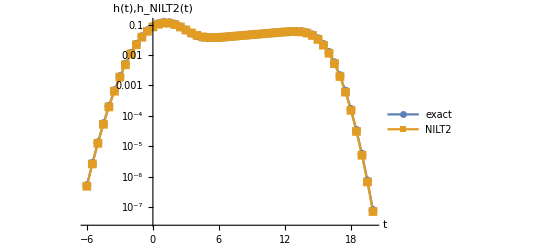

c:/temp/aa/mfm_log.pdf

```mathematica
ListLogPlot[{res,reslt},Joined->True,PlotRange->All,PlotMarkers->Automatic,PlotLegends->Placed[{"exact","NILT2"},{0.8,0.25}],AxesLabel->{"t","h(t),h_NILT2(t)"}]
Export["c:/temp/aa/mfm_log.pdf", %]
```

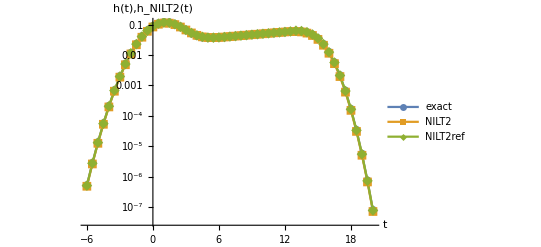

c:/temp/aa/mfm_log_r.pdf

```mathematica
ListLogPlot[{res,reslt,resltr},Joined->True,PlotRange->All,PlotMarkers->Automatic,PlotLegends->Placed[{"exact","NILT2","NILT2ref"},{0.8,0.25}],AxesLabel->{"t","h(t),h_NILT2(t)"}]
Export["c:/temp/aa/mfm_log_r.pdf", %]
```

```mathematica
r1abs=Table[{res[[n,1]],Abs[res[[n,2]] -reslt[[n,2]] ]/res[[n,2]]},{n,1,Length[res]}]
r1rabs=Table[{res[[n,1]],Abs[res[[n,2]] -resltr[[n,2]] ]/res[[n,2]]},{n,1,Length[res]}]
```

{{-6.,0.0470469},{-5.5,0.0470235},{-5.,0.0469934},{-4.5,0.0469729},{-4.,0.0469312},{-3.5,0.0468911},{-3.,0.0468243},{-2.5,0.0467321},{-2.,0.0466152},{-1.5,0.0464286},{-1.,0.0461442},{-0.5,0.0456887},{0.,0.0449418},{0.5,0.0436538},{1.,0.0413809},{1.5,0.0372713},{2.,0.0299091},{2.5,0.0174665},{3.,0.000596869},{3.5,0.0199587},{4.,0.0311447},{4.5,0.0289678},{5.,0.0192043},{5.5,0.0100394},{6.,0.00448454},{6.5,0.00185841},{7.,0.000770647},{7.5,0.00035775},{8.,0.000196205},{8.5,0.000123819},{9.,0.0000840449},{9.5,0.0000555188},{10.,0.0000228232},{10.5,0.0000465188},{11.,0.000254873},{11.5,0.000901689},{12.,0.00266106},{12.5,0.00663104},{13.,0.0136709},{13.5,0.0235289},{14.,0.0346798},{14.5,0.0452381},{15.,0.0540238},{15.5,0.0607461},{16.,0.0656615},{16.5,0.0691794},{17.,0.071703},{17.5,0.0735194},{18.,0.0748422},{18.5,0.0758276},{19.,0.07657},{19.5,0.0771363},{20.,0.0775755}}

{{-6.,0.00188882},{-5.5,0.00182123},{-5.,0.00188352},{-4.5,0.0018074},{-4.,0.00179136},{-3.5,0.00179248},{-3.,0.00176047},{-2.5,0.00176403},{-2.,0.00169787},{-1.5,0.00165212},{-1.,0.00159384},{-0.5,0.0013986},{0.,0.00113832},{0.5,0.000739376},{1.,0.00015008},{1.5,0.00163995},{2.,0.00384536},{2.5,0.00403075},{3.,0.000596869},{3.5,0.0199587},{4.,0.0311447},{4.5,0.0289678},{5.,0.0192043},{5.5,0.0100394},{6.,0.00448454},{6.5,0.00185841},{7.,0.000770647},{7.5,0.00035775},{8.,0.000196205},{8.5,0.000123819},{9.,0.0000840449},{9.5,0.0000555188},{10.,0.0000228232},{10.5,0.0000465188},{11.,0.000254873},{11.5,0.000901689},{12.,0.00266106},{12.5,0.00758276},{13.,0.0509822},{13.5,0.0438794},{14.,0.0364126},{14.5,0.0313566},{15.,0.0262245},{15.5,0.0211939},{16.,0.0166654},{16.5,0.0127366},{17.,0.0095783},{17.5,0.00707026},{18.,0.00509279},{18.5,0.00367198},{19.,0.00262529},{19.5,0.0018968},{20.,0.00139653}}

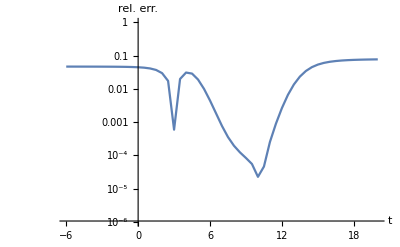

c:/temp/aa/mfm_relerr.pdf

```mathematica
ListLogPlot[{r1abs},Joined->True,(* PlotLegends->Placed[{"NILT2","NILT2ref"},{0.85,0.25}],*) AxesLabel->{"t","rel. err."},PlotRange->{10^-6,1},Ticks->{Automatic,{0.00001,0.001,0.1 }}]
Export["c:/temp/aa/mfm_relerr.pdf", %]
```

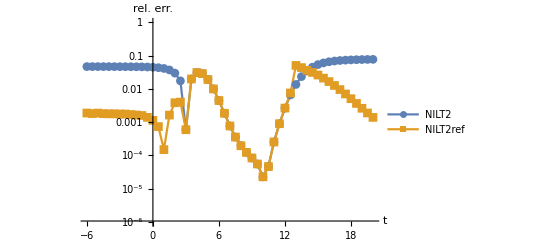

c:/temp/aa/mfm_relerr_r.pdf

```mathematica
ListLogPlot[{r1abs,r1rabs},Joined->True,PlotLegends->Placed[{"NILT2","NILT2ref"},{0.85,0.25}],PlotMarkers->{Automatic},AxesLabel->{"t","rel. err."},PlotRange->{10^-6,1},Ticks->{Automatic,{0.00001,0.001,0.1 }}]
Export["c:/temp/aa/mfm_relerr_r.pdf", %]
```